# Cuaderno de Prácticas

## Álgebra

## Grado en Ingeniería Informática

## CURSO 2025/26

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas :1

## Práctica 7

```mathematica
(* NColoraciones *)
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
(* NumeroCromatico *)
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
(* D3 *)
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
(* QuitarVerticesGrado210 *)
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
(**)
```

```mathematica
<<"Combinatorica`";
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

```mathematica
(* K33 *)
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
(* HomeoMorfoK5K33 *)
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
(* Plano *)
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
(* Conexo *)
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
(* Arbol *)
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
(**)

MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
(**)
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

### Ejercicio 1 Se pide: i. Calcular el número cromático y una coloración óptima ii. Determinar si es plano iii. Comprobar si es un árbol Dados los siguientes grafos

#### a) Cada uno de los grafos del ejercicio 5.29 del manual de prácticas

```mathematica
WG1={2,6,8,0,,"m","a","r","t","i","n","l","u","s"};
FG1={ 
	{0,"a"},{0,"i"},{0,"u"},
	{2,"a"},{2,"i"},{2,"u"},
	{6,"a"},{6,"i"},{6,"u"},
	{8,"a"},{8,"i"},{8,"u"},
	{2,6},{2,8},{2,6}
	};
WG2={2,6,8,0,,"m","a","r","t","i","n","l","u","s"};
FG2={
	{"a","m"},{"a","r"},{"a","t"},{"a","n"},{"a","l"},{"a","s"},
	{"i","m"},{"i","r"},{"i","t"},{"i","n"},{"i","l"},{"i","s"},
	{"u","m"},{"u","r"},{"u","t"},{"u","n"},{"u","l"},{"u","s"}
	};
WG3={1,2,3,4,5,6};
FG3={1->2,3->1,4->5,6->1};
WG4={1,2,3,4};
FG4={2->1,4->1,1->2,3->2,2->3,4->3,1->4,3->4};
WG5={1,2,3,4,5};
FG5={1->4,1->5,2->4,2->5,3->4,3->5};
WG6={1,2,3,4,5,6,7,8};
FG6={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->4,2->7,3->6,5->8};
WG7={1,2,3,4};
FG7={1->2,2->3,3->1,1->4,2->4,3->4};
WG8={1,2,3,4,5,6,7,8,9,10};
FG8={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}};
WG9={1,2,3,4,5,6};
FG9={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,4},{2,5},{3,6}};
```

Comatico y coloración optima

G1

NCOLORACIONES[{{0,1,1,0,0,0,1,0,0,1,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]

3

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Verde

Vértice 8, color Negro

Vértice 9, color Negro

Vértice 10, color Verde

Vértice 11, color Negro

Vértice 12, color Negro

Vértice 13, color Verde

Vértice 14, color Negro

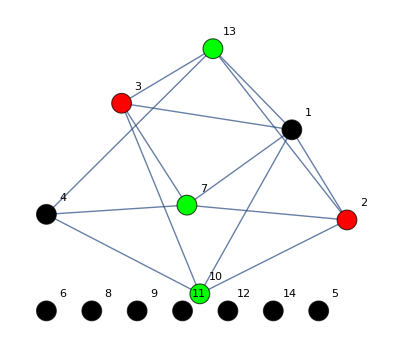

G2

NCOLORACIONES[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Rojo

Vértice 8, color Negro

Vértice 9, color Negro

Vértice 10, color Rojo

Vértice 11, color Negro

Vértice 12, color Negro

Vértice 13, color Rojo

Vértice 14, color Negro

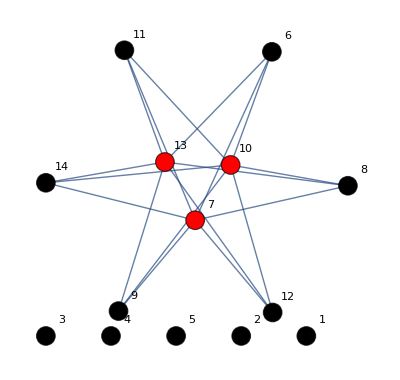

G3

NCOLORACIONES[{{0,1,1,0,0,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,1,0,0},{1,0,0,0,0,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Rojo

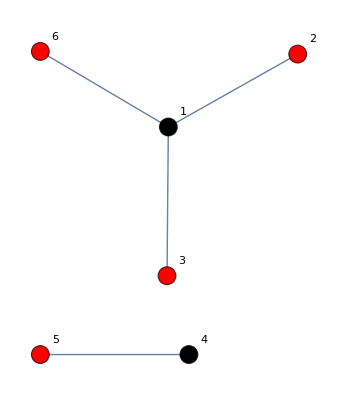

G4

NCOLORACIONES[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

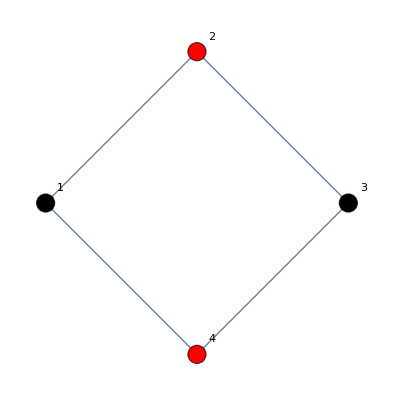

G5

NCOLORACIONES[{{0,0,0,1,1},{0,0,0,1,1},{0,0,0,1,1},{1,1,1,0,0},{1,1,1,0,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

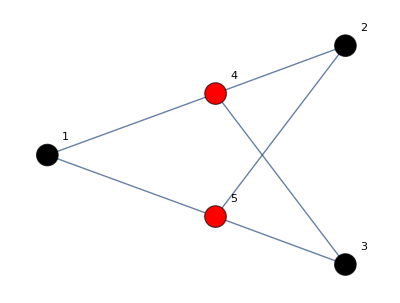

G6

NCOLORACIONES[{{0,1,0,1,0,0,0,1},{1,0,1,0,0,0,1,0},{0,1,0,1,0,1,0,0},{1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1},{0,0,1,0,1,0,1,0},{0,1,0,0,0,1,0,1},{1,0,0,0,1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

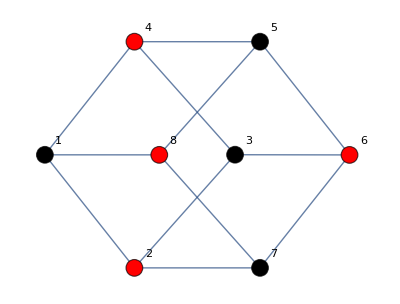

G7

NCOLORACIONES[{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}]

4

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

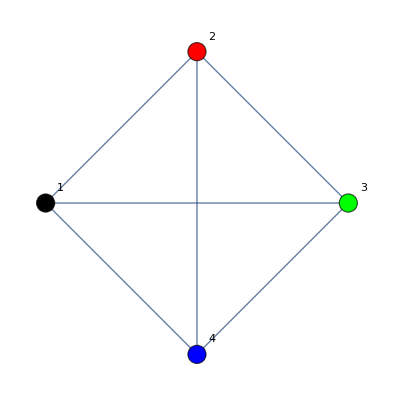

G8

NCOLORACIONES[{{0,1,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

Vértice 9, color Negro

Vértice 10, color Rojo

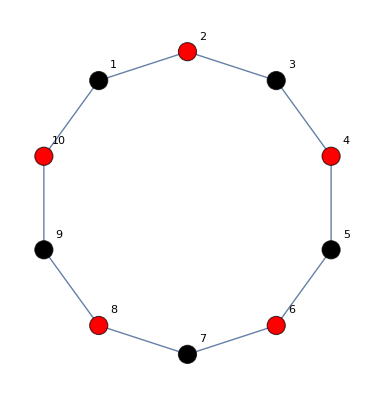

G9

NCOLORACIONES[{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

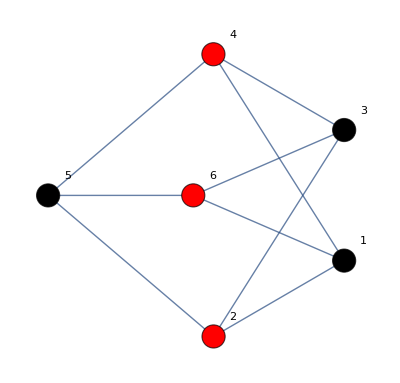

```mathematica
"Comatico y coloración optima"
"G1"
AG1=MATRIZADYACENCIA[WG1,FG1];
NCOLORACIONES[AG1]
NUMEROCROMATICO[AG1]
DIBUJAR[AG1]
"G2"
AG2=MATRIZADYACENCIA[WG2,FG2];
NCOLORACIONES[AG2]
NUMEROCROMATICO[AG2]
DIBUJAR[AG2]
"G3"
AG3=MATRIZADYACENCIA[WG3,FG3];
NCOLORACIONES[AG3]
NUMEROCROMATICO[AG3]
DIBUJAR[AG3]
"G4"
AG4=MATRIZADYACENCIA[WG4,FG4];
NCOLORACIONES[AG4]
NUMEROCROMATICO[AG4]
DIBUJAR[AG4]
"G5"
AG5=MATRIZADYACENCIA[WG5,FG5];
NCOLORACIONES[AG5]
NUMEROCROMATICO[AG5]
DIBUJAR[AG5]
"G6"
AG6=MATRIZADYACENCIA[WG6,FG6];
NCOLORACIONES[AG6]
NUMEROCROMATICO[AG6]
DIBUJAR[AG6]
"G7"
AG7=MATRIZADYACENCIA[WG7,FG7];
NCOLORACIONES[AG7]
NUMEROCROMATICO[AG7]
DIBUJAR[AG7]
"G8"
AG8=MATRIZADYACENCIA[WG8,FG8];
NCOLORACIONES[AG8]
NUMEROCROMATICO[AG8]
DIBUJAR[AG8]
"G9"
AG9=MATRIZADYACENCIA[WG9,FG9];
NCOLORACIONES[AG9]
NUMEROCROMATICO[AG9]
DIBUJAR[AG9]
```

Plano

G1

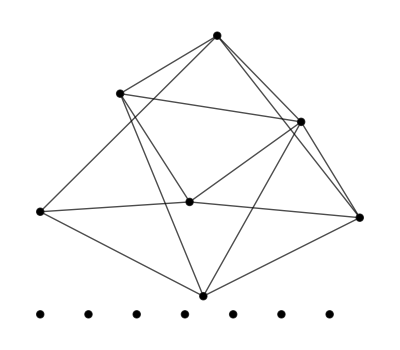

False

G2

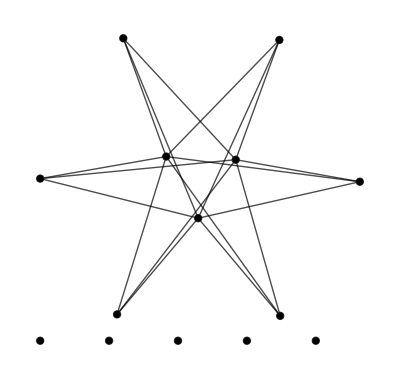

False

G3

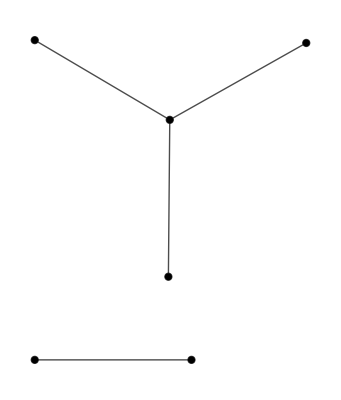

True

G4

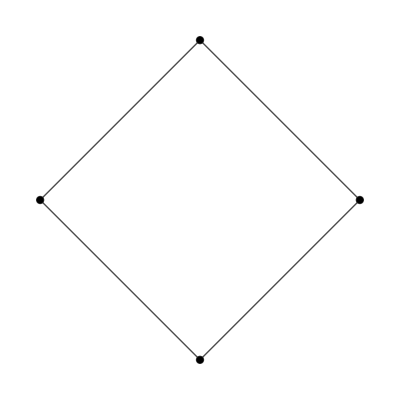

True

G5

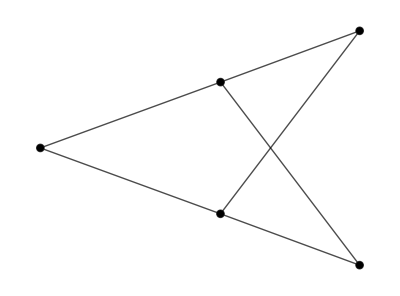

True

G6

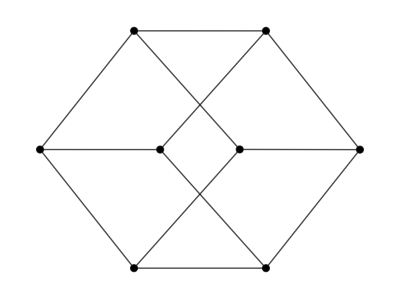

True

G7

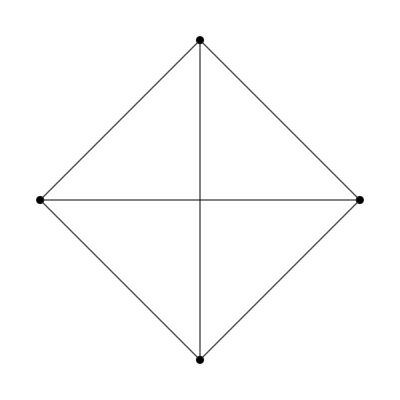

True

G1

-Graphics-

False

G8

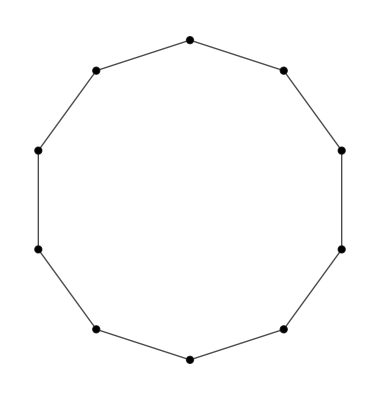

True

G9

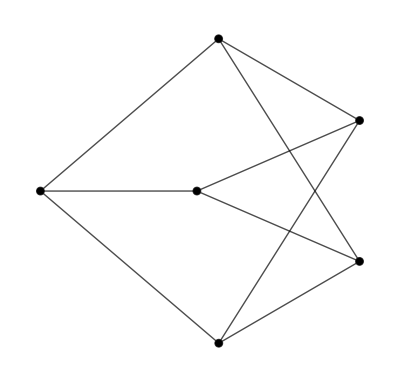

False

```mathematica
"Plano"
"G1"
GraphPlot[AG1,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG1]
"G2"
GraphPlot[AG2,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG2]
"G3"
GraphPlot[AG3,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG3]
"G4"
GraphPlot[AG4,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG4]
"G5"
GraphPlot[AG5,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG5]
"G6"
GraphPlot[AG6,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG6]
"G7"
GraphPlot[AG7,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG7]
"G1"
GraphPlot[AG1,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG1]
"G8"
GraphPlot[AG8,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG8]
"G9"
GraphPlot[AG9,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG9]
```

```mathematica
"Arbol"
"G1"
ARBOL[AG1]
"G2"
ARBOL[AG2]
"G3"
ARBOL[AG3]
"G4"
ARBOL[AG4]
"G5"
ARBOL[AG5]
"G6"
ARBOL[AG6]
"G7"
ARBOL[AG7]
"G8"
ARBOL[AG8]
"G9"
ARBOL[AG9]
```

Arbol

G1

False

G2

False

G3

False

G4

False

G5

False

G6

False

G7

False

G8

False

G9

False

#### b) Cada uno de los grafos del ejercicio 6.8 del manual de prácticas

```mathematica
Eje68G1Adya=({{0, 1, 1, 0, 0, 1}, {1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 0, 0}});
Eje68G2Adya=({{0, 1, 0, 1}, {1, 0, 1, 0}, {0, 1, 0, 1}, {1, 0, 1, 0}});
Eje68G3Adya=({{0, 0, 0, 1, 1}, {0, 0, 0, 1, 1}, {0, 0, 0, 1, 1}, {1, 1, 1, 0, 0}, {1, 1, 1, 0, 0}});
Eje68G4Adya=({{0, 1, 0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 1, 0}, {0, 1, 0, 1, 0, 1, 0, 0}, {1, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 1, 0, 1}, {0, 0, 1, 0, 1, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0, 1, 0}});
Eje68G5Adya=({{0, 1, 1, 1}, {1, 0, 1, 1}, {1, 1, 0, 1}, {1, 1, 1, 0}});
```

```mathematica
"Eje68 G1"
NCOLORACIONES[Eje68G1Adya]
NUMEROCROMATICO[Eje68G1Adya]
"Plano"
PLANO[Eje68G1Adya]
"Arbol"
ARBOL[Eje68G1Adya]
DIBUJAR[Eje68G1Adya]
"Eje68 G2"
NCOLORACIONES[Eje68G2Adya]
NUMEROCROMATICO[Eje68G2Adya]
"Plano"
PLANO[Eje68G2Adya]
"Arbol"
ARBOL[Eje68G2Adya]
DIBUJAR[Eje68G2Adya]
"Eje68 G3"
NCOLORACIONES[Eje68G3Adya]
NUMEROCROMATICO[Eje68G3Adya]
"Plano"
PLANO[Eje68G3Adya]
"Arbol"
ARBOL[Eje68G3Adya]
DIBUJAR[Eje68G3Adya]
"Eje68 G4"
NCOLORACIONES[Eje68G4Adya]
NUMEROCROMATICO[Eje68G4Adya]
"Plano"
PLANO[Eje68G4Adya]
"Arbol"
ARBOL[Eje68G4Adya]
DIBUJAR[Eje68G4Adya]
"Eje68 G5"
NCOLORACIONES[Eje68G5Adya]
NUMEROCROMATICO[Eje68G5Adya]
"Plano"
PLANO[Eje68G5Adya]
"Arbol"
ARBOL[Eje68G5Adya]
DIBUJAR[Eje68G5Adya]
```

Eje68 G1

NCOLORACIONES[{{0,1,1,0,0,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,1,0,0},{1,0,0,0,0,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Rojo

-Graphics-

Eje68 G2

NCOLORACIONES[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

-Graphics-

Eje68 G3

NCOLORACIONES[{{0,0,0,1,1},{0,0,0,1,1},{0,0,0,1,1},{1,1,1,0,0},{1,1,1,0,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

-Graphics-

Eje68 G4

NCOLORACIONES[{{0,1,0,1,0,0,0,1},{1,0,1,0,0,0,1,0},{0,1,0,1,0,1,0,0},{1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1},{0,0,1,0,1,0,1,0},{0,1,0,0,0,1,0,1},{1,0,0,0,1,0,1,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

-Graphics-

Eje68 G5

NCOLORACIONES[{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}]

4

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

-Graphics-

#### c) Un octógono

Octogono

NCOLORACIONES[{{0,1,0,0,0,0,0,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{1,0,0,0,0,0,1,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

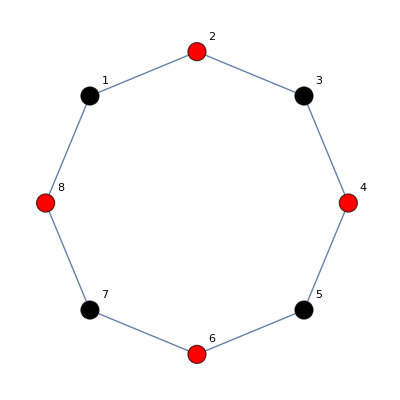

```mathematica
octoAdya=({{0, 1, 0, 0, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 0, 0, 1, 0}});
"Octogono"
NCOLORACIONES[octoAdya]
NUMEROCROMATICO[octoAdya]
"Plano"
PLANO[octoAdya]
"Arbol"
ARBOL[octoAdya]
DIBUJAR[octoAdya]
```

#### d) K7

Octogono

NCOLORACIONES[{{0,1,1,1,1,1,1},{1,0,1,1,1,1,1},{1,1,0,1,1,1,1},{1,1,1,0,1,1,1},{1,1,1,1,0,1,1},{1,1,1,1,1,0,1},{1,1,1,1,1,1,0}}]

7

Plano

False

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

Vértice 5, color Amarillo

Vértice 6, color Cyan

Vértice 7, color Marrón

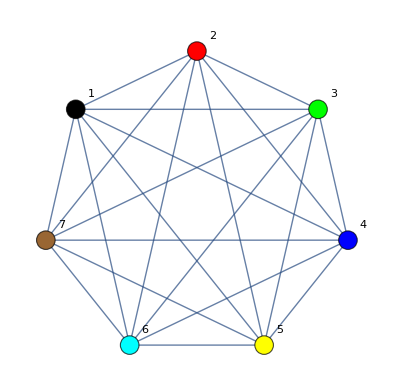

```mathematica
k7Adya=({{0, 1, 1, 1, 1, 1, 1}, {1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1}, {1, 1, 1, 0, 1, 1, 1}, {1, 1, 1, 1, 0, 1, 1}, {1, 1, 1, 1, 1, 0, 1}, {1, 1, 1, 1, 1, 1, 0}});
"Octogono"
NCOLORACIONES[k7Adya]
NUMEROCROMATICO[k7Adya]
"Plano"
PLANO[k7Adya]
"Arbol"
ARBOL[k7Adya]
DIBUJAR[k7Adya]
```

#### e) K4,3

```mathematica
k43Adya=();
"Octogono"
NCOLORACIONES[k43Adya]
NUMEROCROMATICO[k43Adya]
"Plano"
PLANO[k43Adya]
"Arbol"
ARBOL[k43Adya]
DIBUJAR[k43Adya]
```

#### f) Grafo del ejercicio 3 de la convocatoria ordinaria 2 del curso 2023/24

```mathematica
Eje3Ord22324Adya=({{0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}});
```